```mathematica
(*Basic model trajectory*)
ODESystem={
x'[t]==Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
y'[t]==Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
w'[t]==Subscript[Λ, e] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
```

```mathematica
sol1 = NDSolve[{ODESystem/.{Subscript[β, HA]->1/10,Subscript[β, AH]->1/10,Subscript[β, HH]->1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] -> 0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 0, Subscript[Λ, A]->1/10,Subscript[Λ, H]->1/10, Subscript[Λ, e]-> 0}, x[0] == 0, y[0]== 0, w[0]==0}, {x,y, w}, {t, 0, 200}];
```

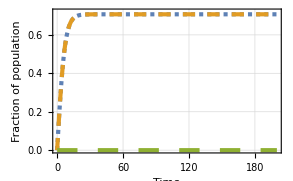

```mathematica
Plot[{Evaluate[x[t]/.sol1[[1,1]]], Evaluate[y[t]/.sol1[[1,2]]], Evaluate[w[t]/.sol1[[1,3]]]}, {t,0,200}, PlotRange->{{0,200},{0.0,0.72}}, PlotStyle->{Dashing[0.01], Dashing[0.03], Dashing[0.05]},PlotLegends->None,PlotTheme->{"Detailed", "ThickLines"},PlotRange->All, ImageSize->1024, FrameLabel->{"Time", "Fraction of population"}, LabelStyle->Directive[Bold, Large]]
```

```mathematica
(*Model with tracking of infections from different sources*)
(*Plotting*)
ODESystem2 = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[Λ, e] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
```

```mathematica
(*No environment, low impact*)
neli = Plot3D[NSolve[{ODESystem2[[1]]==0, ODESystem2[[2]]==0, ODESystem2[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && x[t] ≥ 0} /.{Subscript[β, HA]->1/10,Subscript[β, AH]->par1,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 0, Subscript[Λ, A]->par2,Subscript[Λ, H]->1/10, Subscript[Λ, e]-> 0}, {x[t], y[t], w[t]}, Reals][[1,1,2]],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
ImageSize->Full,AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}];
```

```mathematica
(*No environment, high impact*)
nehi = Plot3D[NSolve[{ODESystem2[[1]]==0, ODESystem2[[2]]==0, ODESystem2[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && x[t] ≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->par1,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->0, Subscript[β, EA]-> 0, Subscript[β, HE] -> 0, Subscript[β, AE] -> 0, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 0, Subscript[Λ, A]->par2,Subscript[Λ, H]->1/10, Subscript[Λ, e]-> 0}, {x[t], y[t], w[t]}, Reals][[1,1,2]],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
ImageSize->Full,AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}];
```

```mathematica
(*Environment low transmission, low impact*)
eltli = Plot3D[NSolve[{ODESystem2[[1]]==0, ODESystem2[[2]]==0, ODESystem2[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && x[t] ≥ 0} /.{Subscript[β, HA]->1/10,Subscript[β, AH]->par1,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/10, Subscript[Λ, A]->par2,Subscript[Λ, H]->1/10, Subscript[Λ, e]-> 1/10}, {x[t], y[t], w[t]}, Reals][[1,1,2]],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
ImageSize->Full,AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}];
```

```mathematica
(*Environment low transmission, high impact*)
elthi = Plot3D[NSolve[{ODESystem2[[1]]==0, ODESystem2[[2]]==0, ODESystem2[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && x[t] ≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->par1,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->1/100, Subscript[β, EA]-> 1/100, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/10, Subscript[Λ, A]->par2,Subscript[Λ, H]->1/10, Subscript[Λ, e]-> 1/10}, {x[t], y[t], w[t]}, Reals][[1,1,2]],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
ImageSize->Full,AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}];
```

```mathematica
(*Environment higher transmission, low impact*)
ehtli = Plot3D[NSolve[{ODESystem2[[1]]==0, ODESystem2[[2]]==0, ODESystem2[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && x[t] ≥ 0} /.{Subscript[β, HA]->1/10,Subscript[β, AH]->par1,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->1/10, Subscript[β, EA]-> 1/10, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/10, Subscript[Λ, A]->par2,Subscript[Λ, H]->1/10, Subscript[Λ, e]-> 1/10}, {x[t], y[t], w[t]}, Reals][[1,1,2]],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
ImageSize->Full,AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}];
```

```mathematica
(*Environment higher transmission, high impact*)
ehthi = Plot3D[NSolve[{ODESystem2[[1]]==0, ODESystem2[[2]]==0, ODESystem2[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && x[t] ≥ 0} /.{Subscript[β, HA]->1/1000,Subscript[β, AH]->par1,Subscript[β, HH]-> 1/10, Subscript[β, AA]-> 1/10,Subscript[β, EH] ->1/10, Subscript[β, EA]-> 1/10, Subscript[β, HE] -> 1/10, Subscript[β, AE] -> 1/10, Subscript[μ, A]->1/10,Subscript[μ, H]->1/10, Subscript[μ, e] -> 1/10, Subscript[Λ, A]->par2,Subscript[Λ, H]->1/10, Subscript[Λ, e]-> 1/10}, {x[t], y[t], w[t]}, Reals][[1,1,2]],{par1,0,1},{par2,0,1}, AxesLabel->{"β_AH","Λ_A", "R_H^*"}, ColorFunction->Function[{x,y,z},Hue[.65(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]], ColorFunctionScaling->False,PlotRange->{{0,1},{0,1},{0.6,1.0}},
ImageSize->Full,AxesStyle->Directive[Bold, FontFamily->"Arial", FontSize->32], LabelStyle->Directive[Bold, FontFamily->"Arial"] , Axes -> True, AxesEdge->{{0,0}, {1,0}, {0,0}}];
GraphicsRow[{neli,eltli, ehtli}] 
GraphicsRow[{nehi, elthi,ehthi}]
```

```mathematica
(*Phase two - try to get at the relative contributions of animals and environment to AMR*)
(*Start by setting RH == 0.7 and solving the equations for RA and RE only *)
ODESystem3 = {
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[Λ, e] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x - Subscript[μ, e]*w[t]
};
```

```mathematica
sol2 = DSolve[{ODESystem3[[1]]==0, ODESystem3[[2]]==0}, {y,w},t, 
Assumptions->{Subscript[β, HA]>0, Subscript[β, AA]>0, Subscript[β, EA]>0, Subscript[β, AE]>0,Subscript[β, HE]>0, Subscript[μ, e]>0, Subscript[μ, A]>0, x>0}];
```

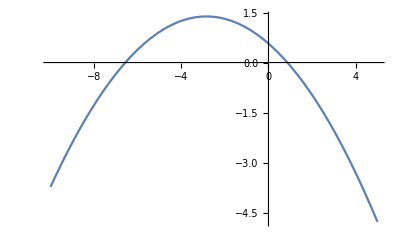

```mathematica
(*This gives us two solutions, with equations of quadratic form. We need to select the 'positive' solution.*)
(*Demonstrate for self satisfaction that we are working with quadratic functions *)
f[y_] := (1-y) * (0.1+0.1*0.7+0.1*y + 0.2 * 2)-0.1*y
Plot[f[w], {w, -10, 5}]
```

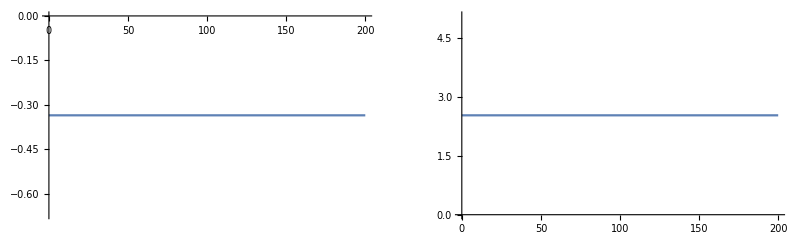

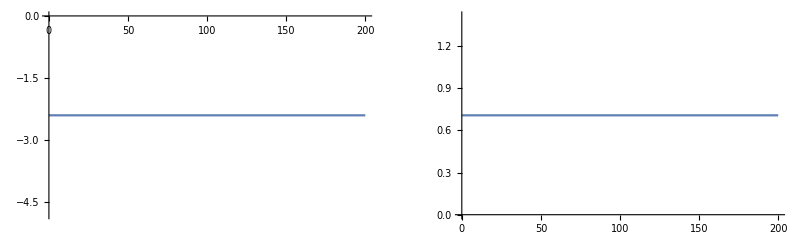

```mathematica
(*Now plot the different solutions to look at what value they are suggesting*)
solv1 = sol2[[1]];
solv2 = sol2[[2]];
wv1 = Plot[Evaluate[w[t]/.solv1[[1]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10, Subscript[Λ, A]-> 0.1, x->.7,  Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.1}], {t,0,200}];
wv2 = Plot[Evaluate[w[t]/.solv2[[1]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10, Subscript[Λ, A]-> 0.1, x->.7, Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.1}], {t,0,200}];
GraphicsRow[{wv1, wv2}]
yv1 = Plot[Evaluate[y[t]/.solv1[[2]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0, Subscript[Λ, A]-> 0.1, x->.7, w-> 2, Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.1}], {t,0,200}];
yv2 = Plot[Evaluate[y[t]/.solv2[[2]] /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0, Subscript[Λ, A]-> 0.1, x->.7, Subscript[β, HE]->0.1, Subscript[β, AE]-> 0.1, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.1}], {t,0,200}];
GraphicsRow[{yv1, yv2}]
(*Solution two is the (biologically speaking) right solution. Now Try to simplify.*)
```

```mathematica
yorigeq = solv2[[2, 2, 2]]
```

(β_AE β_EA-x β_EA β_HE-β_EA Λ_e+β_AA μ_e-x β_HA μ_e-Λ_A μ_e-μ_A μ_e+√(-4 (β_AE β_EA+β_AA μ_e) (-x β_EA β_HE-β_EA Λ_e-x β_HA μ_e-Λ_A μ_e)+(-β_AE β_EA+x β_EA β_HE+β_EA Λ_e-β_AA μ_e+x β_HA μ_e+Λ_A μ_e+μ_A μ_e)^2))/(2 (β_AE β_EA+β_AA μ_e))

```mathematica
yeq= FullSimplify[yorigeq]
```

-(-β_AE β_EA+x β_EA β_HE+β_EA Λ_e-β_AA μ_e+x β_HA μ_e+Λ_A μ_e+μ_A μ_e-√(4 (β_AE β_EA+β_AA μ_e) (β_EA (x β_HE+Λ_e)+(x β_HA+Λ_A) μ_e)+(-β_AE β_EA+β_EA (x β_HE+Λ_e)+(-β_AA+x β_HA+Λ_A+μ_A) μ_e)^2))/(2 (β_AE β_EA+β_AA μ_e))

```mathematica
worigeq = solv2[[1, 2, 2]]
```

-1/μ_e(-x β_HE-Λ_e-(β_AE^2 β_EA)/(2 (β_AE β_EA+β_AA μ_e))+(x β_AE β_EA β_HE)/(2 (β_AE β_EA+β_AA μ_e))+(β_AE β_EA Λ_e)/(2 (β_AE β_EA+β_AA μ_e))-(β_AA β_AE μ_e)/(2 (β_AE β_EA+β_AA μ_e))+(x β_AE β_HA μ_e)/(2 (β_AE β_EA+β_AA μ_e))+(β_AE Λ_A μ_e)/(2 (β_AE β_EA+β_AA μ_e))+(β_AE μ_A μ_e)/(2 (β_AE β_EA+β_AA μ_e))-(β_AE √(-4 (β_AE β_EA+β_AA μ_e) (-x β_EA β_HE-β_EA Λ_e-x β_HA μ_e-Λ_A μ_e)+(-β_AE β_EA+x β_EA β_HE+β_EA Λ_e-β_AA μ_e+x β_HA μ_e+Λ_A μ_e+μ_A μ_e)^2))/(2 (β_AE β_EA+β_AA μ_e)))

```mathematica
(*This equation is much better than the original*)
weq = FullSimplify[worigeq]
```

(β_AE^2 β_EA+2 β_AA (x β_HE+Λ_e) μ_e+β_AE (β_EA (x β_HE+Λ_e)+β_AA μ_e-(x β_HA+Λ_A+μ_A) μ_e)+β_AE √(4 (β_AE β_EA+β_AA μ_e) (β_EA (x β_HE+Λ_e)+(x β_HA+Λ_A) μ_e)+(-β_AE β_EA+β_EA (x β_HE+Λ_e)+(-β_AA+x β_HA+Λ_A+μ_A) μ_e)^2))/(2 μ_e (β_AE β_EA+β_AA μ_e))

```mathematica
(*Define functions so that we can make plots*)
yfunc[xs_, bea_, bhe_, bae_, mue_, Le_] := yeq /. {Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> bea, Subscript[Λ, A]-> 1/10, x->xs, Subscript[β, HE]->bhe, Subscript[β, AE]-> bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->Le};
wfunc[xs_,bea_, bhe_, bae_, mue_, Le_]:= weq/.{Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1bea, Subscript[Λ, A]-> 1/10, x->xs, Subscript[β, HE]->bhe, Subscript[β, AE]-> bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->Le};
```

```mathematica
(*Increasing contribution of environment as human infection increases - animal population is more limited?*) Manipulate[Plot[{yfunc[par1, bea, bhe, bae, mue, Le], wfunc[par1, bea, bhe, bae, mue, Le]},{par1,0,1}, AxesLabel->{"R_H^*", "R^*"}, PlotRange->{{0,1},{0,3}}], {bea, 0, 1}, {bhe, 0, 1},{bae, 0, 1}, {mue, 0, 1.0}, {Le, 0, 0.1}]
```

```mathematica
(*StreamPlot. Very slow, don't always run this*)
Manipulate[StreamPlot[ODESystem3/.{Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> bea, Subscript[Λ, A]-> 0.1, x-> xs, Subscript[β, HE]->bhe, Subscript[β, AE]->bae, Subscript[μ, e]-> mue, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->Le}, {y[t],0,1}, {w[t], 0, 4}], {xs, 0, 1}, {bea, 0, 1}, {bhe, 0, 1},{bae, 0, 1}, {mue, 0, 1.0}, {Le, 0, 1}]
```

```mathematica
(*Solve analytical solutions for x*)
yeqx = Solve[yeq==y, x];
ytargfixedx= Solve[0.7 == yeqx[[1,1,2]], y];
ytargfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001} (*find right solution*)
```

{{y→-2.19756},{y→0.721322}}⟦i,1,2⟧

```mathematica
ytf = Plot3D[Evaluate[ytargfixedx[[2,1,2]]/.{Subscript[Λ, A] -> par1, Subscript[β, HE]-> par2, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_A"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]];
```

```mathematica
weqx = Solve[{w == weq}, x];
weqx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001, w -> 2} (*which solution is positive?*)
```

{{x→16.9402},{x→-223.95}}⟦i,1,2⟧

```mathematica
wtargfixedx = Solve[0.7==weqx[[1,1,2]], w];
(*which solution is the right one*) 
wtargfixedx[[i,1,2]]/.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}
```

{{w→-0.189702},{w→0.16705}}⟦i,1,2⟧

```mathematica
wtf = Plot3D[Evaluate[wtargfixedx[[2,1,2]]/.{Subscript[Λ, A] -> par1, Subscript[β, HE]-> par2, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_E"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]];
```

```mathematica
(* for a lower x *)
ylowfixedx= Solve[yeqx[[1,1,2]]==0.1 , y];
ylowfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001} (*find right solution*)
```

{{y→0.647786},{y→-1.52996}}⟦i,1,2⟧

```mathematica
ylf = Plot3D[Evaluate[ylowfixedx[[1,1,2]]/.{Subscript[Λ, A] -> par1, Subscript[β, HE]-> par2, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_A"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]];
```

```mathematica
wlowfixedx= Solve[weqx[[1,1,2]]==0.1 , w];
wlowfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001} (*find right solution*)
```

{{w→-0.174773},{w→0.0913961}}⟦i,1,2⟧

```mathematica
wlf = Plot3D[Evaluate[wlowfixedx[[2,1,2]]/.{Subscript[Λ, A] -> par1, Subscript[β, HE]-> par2, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_E"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]];
```

```mathematica
yhighfixedx= Solve[yeqx[[1,1,2]]==0.99 , y];
yhighfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001} (*find right solution*)
```

{{y→0.746089},{y→-2.50946}}⟦i,1,2⟧

```mathematica
yhf = Plot3D[Evaluate[yhighfixedx[[1,1,2]]/.{Subscript[Λ, A] -> par1, Subscript[β, HE]-> par2, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_A"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]];
```

```mathematica
whighfixedx= Solve[weqx[[1,1,2]]==0.99 , w];
whighfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001} (*find right solution*)
```

{{w→-0.1956},{w→0.2023}}⟦i,1,2⟧

```mathematica
whf = Plot3D[Evaluate[whighfixedx[[2,1,2]]/.{Subscript[Λ, A] -> par1, Subscript[β, HE]-> par2, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.5, Subscript[μ, e]-> 0.5, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_E"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]];
```

```mathematica
GraphicsRow[{ylf, ytf, yhf}] 
GraphicsRow[{wlf, wtf, whf}]
```

```mathematica
(*-practice-*)
weqx
```

{{x→1/(2 β_HE (-β_AE β_HA+β_AA β_HE))(β_AE^2 β_HA-β_AA β_AE β_HE+w β_AE β_EA β_HE+β_AE β_HE Λ_A+β_AE β_HA Λ_e-2 β_AA β_HE Λ_e+β_AE β_HE μ_A-w β_AE β_HA μ_e+2 w β_AA β_HE μ_e-√((-β_AE^2 β_HA+β_AA β_AE β_HE-w β_AE β_EA β_HE-β_AE β_HE Λ_A-β_AE β_HA Λ_e+2 β_AA β_HE Λ_e-β_AE β_HE μ_A+w β_AE β_HA μ_e-2 w β_AA β_HE μ_e)^2-4 β_HE (-β_AE β_HA+β_AA β_HE) (-w β_AE^2 β_EA-β_AE^2 Λ_A+β_AA β_AE Λ_e-w β_AE β_EA Λ_e-β_AE Λ_A Λ_e+β_AA Λ_e^2-β_AE Λ_e μ_A-w β_AA β_AE μ_e+w^2 β_AE β_EA μ_e+w β_AE Λ_A μ_e-2 w β_AA Λ_e μ_e+w β_AE μ_A μ_e+w^2 β_AA μ_e^2)))},{x→1/(2 β_HE (-β_AE β_HA+β_AA β_HE))(β_AE^2 β_HA-β_AA β_AE β_HE+w β_AE β_EA β_HE+β_AE β_HE Λ_A+β_AE β_HA Λ_e-2 β_AA β_HE Λ_e+β_AE β_HE μ_A-w β_AE β_HA μ_e+2 w β_AA β_HE μ_e+√((-β_AE^2 β_HA+β_AA β_AE β_HE-w β_AE β_EA β_HE-β_AE β_HE Λ_A-β_AE β_HA Λ_e+2 β_AA β_HE Λ_e-β_AE β_HE μ_A+w β_AE β_HA μ_e-2 w β_AA β_HE μ_e)^2-4 β_HE (-β_AE β_HA+β_AA β_HE) (-w β_AE^2 β_EA-β_AE^2 Λ_A+β_AA β_AE Λ_e-w β_AE β_EA Λ_e-β_AE Λ_A Λ_e+β_AA Λ_e^2-β_AE Λ_e μ_A-w β_AA β_AE μ_e+w^2 β_AE β_EA μ_e+w β_AE Λ_A μ_e-2 w β_AA Λ_e μ_e+w β_AE μ_A μ_e+w^2 β_AA μ_e^2)))}}

```mathematica
Plot3D[Evaluate[yfixedx/.{Subscript[Λ, A] -> par1, Subscript[β, HE]-> par2}][[8,2]], {par1,0,1}, {par2, 0, 1}, AxesLabel->{"Λ_A", "β_HE", "R_A"}, ColorFunction->Function[{x,y,z},Hue[.2(1-Rescale[z, {0.6180339887498953, 0.9},{0,1}])]]]
```

```mathematica
Evaluate[wfixedx[[1,2]]/.{Subscript[Λ, A] -> par1, Subscript[β, HE]-> par2, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 1/10, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.1, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.1}]
```

{{w→2.38095 (0.354-1.1 par1+2.17 par2-1. √((-0.354+1.1 par1-2.17 par2)^2-0.84 (-0.0617-2.31 par1+0.861 par2-7.7 par1 par2+4.9 par2^2)))},{w→2.38095 (0.354-1.1 par1+2.17 par2+√((-0.354+1.1 par1-2.17 par2)^2-0.84 (-0.0617-2.31 par1+0.861 par2-7.7 par1 par2+4.9 par2^2)))}}⟦1,2⟧

```mathematica
Evaluate[wfixedx[[2,1,2]]/.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}]
```

0.16705

```mathematica
yeqx
```

```mathematica
yfixedx
```

{{y→1/(10. β_AE β_EA+10. β_AA μ_e)0.5 (10. β_AE β_EA-7. β_EA β_HE-10. β_EA Λ_e+10. β_AA μ_e-7. β_HA μ_e-10. Λ_A μ_e-10. μ_A μ_e-1. √(-4. (10. β_AE β_EA+10. β_AA μ_e) (-7. β_EA β_HE-10. β_EA Λ_e-7. β_HA μ_e-10. Λ_A μ_e)+(-10. β_AE β_EA+7. β_EA β_HE+10. β_EA Λ_e-10. β_AA μ_e+7. β_HA μ_e+10. Λ_A μ_e+10. μ_A μ_e)^2))},{y→1/(10. β_AE β_EA+10. β_AA μ_e)0.5 (10. β_AE β_EA-7. β_EA β_HE-10. β_EA Λ_e+10. β_AA μ_e-7. β_HA μ_e-10. Λ_A μ_e-10. μ_A μ_e+√(-4. (10. β_AE β_EA+10. β_AA μ_e) (-7. β_EA β_HE-10. β_EA Λ_e-7. β_HA μ_e-10. Λ_A μ_e)+(-10. β_AE β_EA+7. β_EA β_HE+10. β_EA Λ_e-10. β_AA μ_e+7. β_HA μ_e+10. Λ_A μ_e+10. μ_A μ_e)^2))}}

```mathematica
Map[yfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}, {1,2}]
```

{{{y→-2.19756},{y→0.721322}}⟦i,1,2⟧[1],{{y→-2.19756},{y→0.721322}}⟦i,1,2⟧[2]}

```mathematica
yfixedx[[i, 1,2]] /.{Subscript[Λ, A] -> 0.1, Subscript[β, HE]-> 0.1, Subscript[β, HA]->1/10 ,Subscript[β, AA]-> 1/10, Subscript[β, EA]-> 0.1, Subscript[β, AE]-> 0.11, Subscript[μ, e]-> 0.9, Subscript[μ, A]-> 0.1, Subscript[Λ, e]->0.001}
```

{{y→-2.19756},{y→0.721322}}⟦i,1,2⟧

```mathematica
(*Try to solve ODE sys 2 and then have a look at the equation for RH - what's in the denominator?*)
sol3 = DSolve[{ODESystem2[[1]]==0, ODESystem2[[2]]==0, ODESystem2[[3]]==0}, {x,y,w},t, 
Assumptions->{Subscript[β, HA]>0,Subscript[β, AH]>0,Subscript[β, HH]>10, Subscript[β, AA]>10,Subscript[β, EH] > 0, Subscript[β, EA]> 0, Subscript[β, HE] > 0, Subscript[β, AE] > 0, Subscript[μ, A]> 0,Subscript[μ, H]>0, Subscript[μ, e] > 0, Subscript[Λ, A]>0,Subscript[Λ, H]>0, Subscript[Λ, e]>0}];
```

$Aborted

```mathematica
(*Equilibrium analysis for sensitivity analysis*)
ODESystem3 = {
Subscript[Λ, H]*(1-x[t])+Subscript[β, AH]*y[t]*(1-x[t])+Subscript[β, HH]*x[t]*(1-x[t]) + Subscript[β, EH]*w[t] * (1 - x[t])-Subscript[μ, H]*x[t],
Subscript[Λ, A]*(1-y[t])+Subscript[β, HA]*x[t]*(1-y[t])+Subscript[β, AA]*y[t]*(1-y[t]) + Subscript[β, EA]*w[t] * (1 - y[t])-Subscript[μ, A]*y[t],
Subscript[γ, A]*Subscript[Λ, A]+Subscript[γ, H]*Subscript[Λ, H] + Subscript[β, AE]*y[t] + Subscript[β, HE] * x[t] - Subscript[μ, e]*w[t]
};
equilibrium[LamH_,LamA_,gamH_,gamA_,betHH_,betAA_,betAH_,betEH_,betHA_,betEA_,betHE_,betAE_,muH_,muA_,muE_]:= NSolve[{ODESystem3[[1]]==0, ODESystem3[[2]]==0, ODESystem3[[3]]==0 && x[t] ≥ 0 && y[t] ≥ 0 && w[t] ≥ 0} /.{Subscript[Λ, H]->LamH,Subscript[Λ, A]->LamA, Subscript[γ, A]-> gamA, Subscript[γ, H]-> gamH,Subscript[β, HH]-> betHH, Subscript[β, AA]-> betAA,Subscript[β, AH]->betAH,Subscript[β, EH] ->betEH, Subscript[β, HA]->betHA, Subscript[β, EA]-> betEA, Subscript[β, HE] -> betHE, Subscript[β, AE] -> betAE, Subscript[μ, A]->muA,Subscript[μ, H]->muH, Subscript[μ, e] -> muE}, {x[t], y[t], w[t]}, Reals][[1, 1, 2]]
```

```mathematica
parameters = Rest[Import["M:\\New projects\\Model env compartment\\paramodel.csv"]]
```

{{1,0.996401,0.992257,0.00982318,0.986369,0.983315,0.0176817,0.979826,0.977749,0.9759,0.0251963,0.0263904,0.973477,0.0271597,0.027699,0.0275059},9169,{9171,0.00359869,0.00774264,0.990177,0.0136314,0.0166848,0.982318,0.0201745,0.0222513,0.0241003,0.974804,0.97361,0.0265226,0.97284,0.972301,0.972495}}
 |  |  |  |

```mathematica
eqanalysis = Table[equilibrium[parameters[[x, 2]], parameters[[x, 3]], parameters[[x, 4]], parameters[[x, 5]], parameters[[x, 6]], 
parameters[[x, 7]], parameters[[x, 8]], parameters[[x, 9]], parameters[[x, 10]],parameters[[x, 11]], parameters[[x, 12]], 
parameters[[x, 13]], parameters[[x, 14]], parameters[[x, 15]], parameters[[x,16]]],{x, 1, Length[parameters]}];
```

```mathematica
Dimensions[eqanalysis]
```

{9171}

```mathematica
Export["M:\\New projects\\Model env compartment\\outcomeequilibrium.csv", eqanalysis];
```

```mathematica
Which[parameters[[1,2]]==1, parameters[[1,3]] < 1]
```

```mathematica
a=2;Which[a==1,x,a==2,b]
```

b

```mathematica
Which[a==1,x,a==2, b, a == 4, c]
```

b

```mathematica
Do[If[!NumericQ[eqanalysis[[x]] ], Print[x]], {x, 1, Length[eqanalysis]}]
```

2110

4005

4148

6043

8081

8224

```mathematica
parameters[[8224]]
```

{8224,0.922137,0.774046,0.526523,0.0679389,0.282334,0.596267,0.329771,0.462369,0.231516,0.95877,0.892366,0.859528,0.760798,0.412759,0}